4.1777

-3.73923

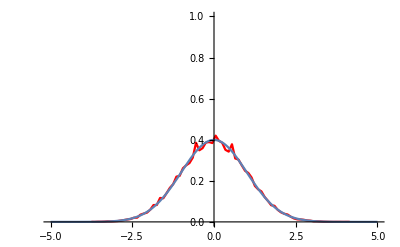

```mathematica
data=Import["/home/petergu/MyHome/USTCcomputer/2019Autumn/CompPhys/HW9/data.csv"];
data=Flatten[data];
Max[data]
Min[data]
(*Histogram[data,{1},PlotRange->{{-100,100},{0,10000}}]*)
p=HistogramList[data,{.1}];
bin=p[[1]];
binmid=Range[Length[bin]-1];
For[i=1,i<Length[bin],i++,
binmid[[i]]=(bin[[i]]+bin[[i+1]])/2;
];
Length[binmid];
cnt=p[[2]]/(Length[data]*(.1));
his=ListLinePlot[Transpose[{binmid,cnt}],PlotRange->{{-5,5},{0,1}},PlotStyle->RGBColor["Red"]];
real=Plot[1/(√(2π))Exp[-x^2/2],{x,-5,5},PlotRange->All];
Show[his,real]
```